```mathematica
cubeWithHoles[R_,L_,center1_,center2_,r1_,r2_,n_]:=Module[{point,points={}},While[Length[points]<n,point=RandomReal[{-L,L},3];
If[Norm[point-center1]>=r1&&Norm[point-center2]>=r2,AppendTo[points,point]]];
points]

(*Example Usage*)
points=cubeWithHoles[1,2,{-1,0,0},{1,0,0},0.5,0.5,1000];
```

```mathematica
ListPointPlot3D[points,BoxRatios->{1,1,1},PlotStyle->{Red,PointSize[Small]}]
```

-Graphics3D-

```mathematica
visualizeCubeWithSpheres[L_,center1_,center2_,r1_,r2_]:=Graphics3D[{Opacity[0.25],Blue,Cuboid[{-L,-L,-L},{L,L,L}],Opacity[0.5],Red,Sphere[center1,r1],Opacity[0.5],Green,Sphere[center2,r2]},Boxed->False,Lighting->"Neutral",Axes->True,AxesOrigin->{0,0,0}]

(*Example Usage*)
visualizeCubeWithSpheres[2,{-1,0,0},{1,0,0},0.5,0.5]
```

-Graphics3D-

```mathematica
Show[%197,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
doubleTorusSample[r1_,r2_,n_]:=Module[{theta,phi,x,y,z,torus1,torus2,chooseTorus},Table[theta=RandomReal[{0,2 Pi}];
phi=RandomReal[{0,2 Pi}];
chooseTorus=RandomChoice[{1,2}];
If[chooseTorus==1,torus1={r1 Cos[theta]+r2 Cos[theta] Cos[phi],r1 Sin[theta]+r2 Sin[theta] Cos[phi],r2 Sin[phi]};
torus1,torus2={r1 Cos[theta]+r2 Cos[theta] Cos[phi]+3 r1,r1 Sin[theta]+r2 Sin[theta] Cos[phi],r2 Sin[phi]};
torus2],n]]

(*Example Usage*)
dTpoints=doubleTorusSample[4,3,1000];
ListPointPlot3D[dTpoints]
```

-Graphics3D-

```mathematica
doubleTorusPlot[r1_,r2_]:=Show[ParametricPlot3D[{r1 Cos[theta]+r2 Cos[theta] Cos[phi],r1 Sin[theta]+r2 Sin[theta] Cos[phi],r2 Sin[phi]},{theta,0,2 Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.5]],ParametricPlot3D[{r1 Cos[theta]+r2 Cos[theta] Cos[phi]+3 r1,r1 Sin[theta]+r2 Sin[theta] Cos[phi],r2 Sin[phi]},{theta,0,2 Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.5]],Boxed->False,Axes->None,PlotRange->All,   ViewPoint->{1.3,-2.4,2.0}]

(*Example Usage*)
doubleTorusPlot[4,3]
```

-Graphics3D-

```mathematica
distsq[p_,q_]:=(p[[1]]-q[[1]])^2+(p[[2]]-q[[2]])^2+(p[[3]]-q[[3]])^2
proxGraph[list_,eps_]:=(size=Length[list];epsq=eps^2;Reap[Do[If[distsq[list[[i]],list[[j]]]<epsq,Sow[Line[{i,j}]]],{i,1,size-1},{j,i+1,size}]][[2,1]])
visualize[ptlist_,eps_]:=MeshRegion[ptlist,proxGraph[ptlist,eps]]
visualize[ptlist_, 0] := ListPointPlot3D[ptlist,BoxRatios->{1,1,1}]
```

```mathematica
Eps = {0, 0.2, 0.4, 0.8, 1.2}
visualize[dTpoints,#] & /@ Eps
```

{0,0.2,0.4,0.8,1.2}

```mathematica
{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}
```

```mathematica
Eps = {0, 0.2, 0.4, 0.8, 1.2}
visualize[points,#] & /@ Eps
```

{0,0.2,0.4,0.8,1.2}

```mathematica
{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}
```

```mathematica
P1={0,0,0}; (*First corner of the cube*)
P2={1,1,1}; (*Opposite corner of the cube*)
cube=Cuboid[P1,P2];

Graphics3D[{Directive[Opacity[0.5],Blue],cube},Axes->True]
```

-Graphics3D-

```mathematica
formatPoint[point_List]:=StringJoin[Riffle[ToString/@point,", "]]

(*Apply the function to all points and export*)
Export["cbPoints.txt",formatPoint/@points,"Lines"]
Export["dtPoints.txt", formatPoint /@ dtPoints, "Lines"]
```

cbPoints.txt

dtPoints.txt

```mathematica
kleinBottle[u_,v_]:={(2/15) Cos[u] (3 Cos[v]-30 Sin[u]+90 Cos[u]^4 Sin[u]-60 Cos[u]^6 Sin[u]+5 Cos[u] Cos[v] Sin[u]),(1/15) Sin[u] (3 Cos[v]-3 Cos[u]^2 Cos[v]-48 Cos[u]^4 Cos[v]+48 Cos[u]^6 Cos[v]-60 Sin[u]+5 Cos[u] Cos[v] Sin[u]-5 Cos[u]^3 Cos[v] Sin[u]-80 Cos[u]^5 Cos[v] Sin[u]+80 Cos[u]^7 Cos[v] Sin[u]),(2/15) (3+5 Cos[u] Sin[u]) Sin[v]};

ParametricPlot3D[kleinBottle[u,v],{u,0,2 Pi},{v,0,2 Pi},PlotPoints->50,Mesh->None,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[kleinBottle[u,v],{u,0,2 π},{v,0,2 π},Mesh->Automatic,MeshFunctions->{#3&},PlotPoints->50,Mesh->None,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[kleinBottle[u,v],{u,0,2 π},{v,0,2 π},Mesh->Automatic,MeshFunctions->Automatic,Mesh->Automatic,MeshFunctions->{#3&},PlotPoints->50,Mesh->None,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[kleinBottle[u,v],{u,0,2 π},{v,0,2 π},PlotTheme->"Scientific",Mesh->Automatic,MeshFunctions->Automatic,Mesh->Automatic,MeshFunctions->{#3&},PlotPoints->50,Mesh->None,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Show[%756,ImageSize->Full]
```

-Graphics3D-

```mathematica
Show[%756,ImageSize->Medium]
```

-Graphics3D-

```mathematica
Show[%756,ViewPoint->Right]
```

-Graphics3D-

```mathematica
Graphics[{(*Draw the rectangle*)EdgeForm[Thick],White,Rectangle[{0,0},{2,1}],(*Label the edges*)Text[Style["A",Red,Bold],{1,1.1}],(*Top edge*)Text[Style["A",Red,Bold],{1,-0.1}],(*Bottom edge*)Text[Style["B",Blue,Bold],{-0.1,0.5}],(*Left edge*)Text[Style["B",Blue,Bold],{2.1,0.5}],(*Right edge*)(*Draw arrows for identification*)Arrow[{{0.5,1.05},{1.5,1.05}}],(*Top edge arrow*)Arrow[{{1.5,-0.05},{0.5,-0.05}}],(*Bottom edge arrow*)Arrow[{{-0.05,0.2},{-0.05,0.8}}],(*Left edge arrow*)Arrow[{{2.05,0.8},{2.05,0.2}}]  (*Right edge arrow*)}]
```

-Graphics-

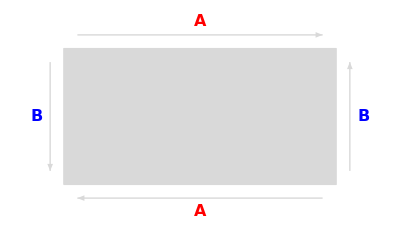

```mathematica
Graphics[{(*Draw the rectangle*)EdgeForm[Thick],LightGray,Rectangle[{0,0},{2,1}],(*Arrows and labels for top and bottom edges (labeled'A')*)Arrow[{{0.1,1.1},{1.9,1.1}}],Arrow[{{1.9,-0.1},{0.1,-0.1}}],Text[Style["A",Red,Bold,16],{1,1.2}],Text[Style["A",Red,Bold,16],{1,-0.2}],(*Arrows and labels for left and right edges (labeled'B')*)Arrow[{{-0.1,0.9},{-0.1,0.1}}],Arrow[{{2.1,0.1},{2.1,0.9}}],Text[Style["B",Blue,Bold,16],{-0.2,0.5}],Text[Style["B",Blue,Bold,16],{2.2,0.5}]}]
```

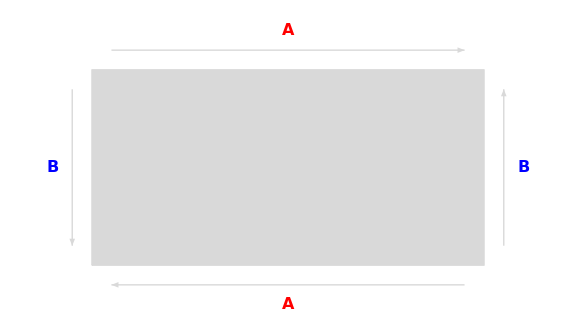

```mathematica
Show[%762,ImageSize->Large]
```